## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_}]:=Module[{gridLabel,gridData},
gridLabel={"k","(X^k)","f(X^k)","Sum[α_i*e_i]"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
For[i=1,i≤Length[points],i++,gridData[[i,4]]="( "<>ToString[SetAccuracy[norms[[i,1]],4]]<>", "<>ToString[SetAccuracy[norms[[i,2]],4]]<>" )"
];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,setX_,setY_,{points_,fValues_}]:=Module[{},
ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
MakeSimplex[Coord_List,L_]:=Module[{j,i,ArrOfPoints=Table[{},{n,1,Length@Coord+1}],Dim=Length@Coord,SimplexSize=Length@Coord+1},
For[i=1,i≤SimplexSize,++i,
For[j=1,j≤Dim,++j,
If[j<i-1,
AppendTo[ArrOfPoints[[i]],Coord[[j]]];
,
If[j>i-1,
AppendTo[ArrOfPoints[[i]],Coord[[j]]-L/(√(2j(j+1)))];
,
AppendTo[ArrOfPoints[[i]],Coord[[j]]+L*√(j/(2(j+1)))];
];
];
];
];
ArrOfPoints
];
```

## Алгоритм

```mathematica
Algorithm[Coord_List,func_,δ_,ϵ_,Len_,Method_List] := Module [{Points={},X,ReflectedX,OldReflX,L=Len,counter=0,FORSHOW={},α,β,γ,MeanX},
X = MakeSimplex[Coord,L];
AppendTo[FORSHOW,X];
If[Method[[1]]=="Nelder-Mid",
α=Method[[2]];
β=Method[[3]];
γ=Method[[4]];
];
(*While[ L>ϵ,*)
MeanX=1/(Length@X-1)Sum[X[[i]],{i,1,Length@X-1}];
While[1/(Length@X)Sum[(func[X[[i]]]-func[MeanX])^2,{i,1,Length@X}]≥ϵ^2,
++counter;
Points = Sort[Table[{X[[i]],func[X[[i]]]},{i,1,Length@X}],#1[[2]]<#2[[2]]&]//N;
MeanX=1/(Length@Points-1)Sum[Points[[i,1]],{i,1,Length@Points-1}];
If[Method[[1]]=="Nelder-Mid",
ReflectedX=MeanX+α(MeanX - Points[[-1,1]]),
ReflectedX=2*MeanX-Points[[-1,1]];
];

If[Method[[1]]=="Nelder-Mid",
OldReflX=ReflectedX;
If[func[OldReflX]<Points[[1,2]],
ReflectedX=MeanX+β(OldReflX-MeanX);
If[func[ReflectedX]<Points[[1,2]],
X =Points[[;;-2,1]]~Join~{ReflectedX},
X =Points[[;;-2,1]]~Join~{OldReflX};
];
];
If[func[OldReflX]>=Points[[-1,2]],
ReflectedX=MeanX+γ(OldReflX-MeanX);
If[func[ReflectedX]<Points[[-1,2]],
X =Points[[;;-2,1]]~Join~{ReflectedX},
X=Map[(Points[[1,1]]+δ(#[[1]]-Points[[1,1]]))&,Points];
],
X=Points[[;;-2,1]]~Join~{OldReflX};
],
If[func[ReflectedX]>Points[[-1,2]],
X=Map[(Points[[1,1]]+δ(#[[1]]-Points[[1,1]]))&,Points];
L=L*δ,
X =Points[[;;-2,1]]~Join~{ReflectedX};
];
];

AppendTo[FORSHOW,X];
];
Points = Sort[Table[{X[[i]],func[X[[i]]]},{i,1,Length@X}],#1[[2]]<#2[[2]]&]//N;
Return[{counter,Points[[1]],FORSHOW}];
];
```

## Функции:

```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
g[{x_,y_}]:=8 x^2+5 y^2-4x y + 8 √5(x+2y)+64;
rosenbrok[{x_,y_}]:=(1-x)^2+(y-x^2)^2;
```

## Вычисления:

```mathematica
(*{"Nelder-Mid",α,β,γ}*)
ϵ=10^-7;
δ=1/3;
LL=0.5;
α=1;
β=3;
γ=1/2;
```

### Первый пример:

```mathematica
(*func =f;(*x0 = {√5,0}, x1 = {0 , 2 √5}*)
Res = Algorithm[{0,2 √5}, func,δ,ϵ,LL,{"Nelder-Mid",α,β,γ}];
Counter= Res[[1]];
M = Res[[2]];
X=Res[[3]];
setX = {x,-5,5};
setY ={y,-5,5};*)
```

### Второй пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
Res = Algorithm[{-1,-2}, func,δ,ϵ,LL,{"Nelder-Mid",α,β,γ}];
Counter= Res[[1]];
M = Res[[2]];
X=Res[[3]];
setX = {x,-4,4};
setY ={y,-4,4};
```

## Результаты:

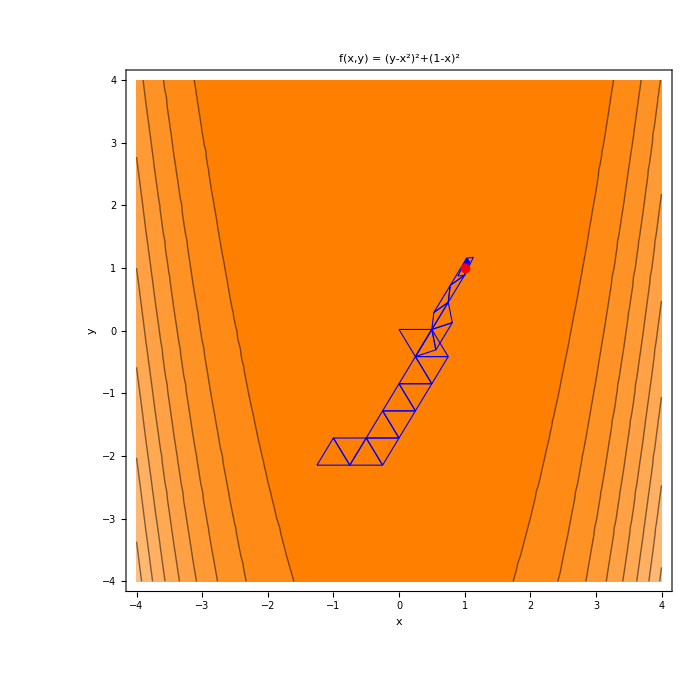

```mathematica
Show[ContourPlot[func[{x,y}],setX,setY,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5 #]],Lighter[Orange,0.5 #]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",func[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->700],(*отрисовываем массив симплексов*)Table[Graphics[{FaceForm[],EdgeForm[Directive[Thick,Dashed,Blue]],Polygon[X[[i]]]}],{i,1,Length[X]}],Graphics[{Red,PointSize[0.01],Point[M[[1]]]}]]
```

```mathematica
M
```

{{0.999809,0.999459},6.17196×10^-8}

```mathematica
Counter
```

54